```mathematica
(*1.grf comstructiom*)
distribution=TransformedDistribution[r Exp[0*I t],{r\[Distributed]NormalDistribution[0 ,1],t\[Distributed]UniformDistribution[{0,2 Pi}]}]; 
grfreset:=Module[{},inpoints={};
inval={};
];
corr[x_]=Exp[-x^2];
grf[newpoint_,lh2_,lv2_]:=Module[{val},
dim=Length[newpoint];
lh=lh2; (*Horizontal scale*)
lv=lv2; (*Vertical scale*)
val=lv*evaluateat[newpoint*1/lh];val];
evaluateat[newpoint_]:=Module[{len,val,check},
{len=Length[inpoints];
If[len==0,{
inpoints={newpoint};
val=RandomVariate[distribution];
inval={val};},

{check=Position[inpoints,newpoint];

If[Length[check]==0,
val=grfadd[newpoint];
If[checkit==0,
{inval=Append[inval,val];
inpoints=Append[inpoints,newpoint];}
];,
{
val=inval[[check[[1,1]]]];}
];
}];
val}
][[1]];
grfadd[newpoint_]:=Module[{len},
len=Length[inpoints];
c0=1;
normm=Sqrt[Total[Abs[Transpose[Transpose[inpoints]-newpoint]]^2,{2}]];
boole=Boole[Negative[normm-5]];(*selects all points from inpoints that are within 5 correlation lengths of the newpoint*)
sel=Flatten[Position[boole,1]];
sellen=Length[sel];

	If[sellen==0,
		{a=RandomVariate[distribution]},
		{invalsel=Table[inval[[ii]],{ii,sel}];
		inpointssel=Table[inpoints[[ii]],{ii,sel}];
		m3=Table[0,{sellen},{sellen}];
		Table[{inplast=inpointssel[[i]] ;
			normm2=Sqrt[Total[Abs[Transpose[Transpose[Take[inpointssel,i]]-inplast]]^2,{2}]];
			normm2=Take[normm2,i-1];
			m3[[i,1;;i-1]]=normm2;
			m3[[1;;i-1,i]]=normm2;
			}
		,{i,2,sellen}];
		csel=corr[m3];
		cjsel=corr[normm[[sel]]];
		fasel=Quiet[LinearSolve[csel,cjsel]];
		fa22sel=1-cjsel.fasel;
		fa2sel=Sqrt[fa22sel];		
		pre=Norm[csel.fasel-cjsel];
		If[Or[pre>10^-12,fa22sel/Norm[fasel]<10^-6],
		{checkit=1;
			fa2sel=0;},checkit=0
		];
a=fa2sel*RandomVariate[distribution]+fasel.invalsel;
}
];
a
];
```

```mathematica
(*2.inflation parameter set*)
φstep=0.05;
m=10^-6;
amp=10^-13;
φmax=30;
φstart=φmax-φstep;
Δt=10^5;
steps=500;
η:=RandomReal[NormalDistribution[0,1/√Δt]];
V0[x1_]:=1/2 m^2 x1^2;
VR=Table[0,{i,steps}];
VR1=Table[0,{i,steps}];
VR2=Table[0,{i,steps}];
VR3=Table[0,{i,steps}];
VR4=Table[0,{i,steps}];
VR5=Table[0,{i,steps}];
VR6=Table[0,{i,steps}];
VR7=Table[0,{i,steps}];
VR8=Table[0,{i,steps}];
VR9=Table[0,{i,steps}];
VR10=Table[0,{i,steps}];
VR11=Table[0,{i,steps}];
VR12=Table[0,{i,steps}];
VR13=Table[0,{i,steps}];
VR14=Table[0,{i,steps}];
VR15=Table[0,{i,steps}];
VR16=Table[0,{i,steps}];
VR17=Table[0,{i,steps}];
VR18=Table[0,{i,steps}];
VR19=Table[0,{i,steps}];
VR20=Table[0,{i,steps}];
VTOTAL=Table[0,{i,steps}];
H=Table[0,{i,steps}];
```

```mathematica
(*3.inflation trajectory*)
φ1=Table[0,{i,steps}];
φ2=Table[0,{i,steps}];
φ3=Table[0,{i,steps}];
φ4=Table[0,{i,steps}];
φ5=Table[0,{i,steps}];
φ6=Table[0,{i,steps}];
φ7=Table[0,{i,steps}];
φ8=Table[0,{i,steps}];
φ9=Table[0,{i,steps}];
φ10=Table[0,{i,steps}];
φ11=Table[0,{i,steps}];
φ12=Table[0,{i,steps}];
φ13=Table[0,{i,steps}];
φ14=Table[0,{i,steps}];
φ15=Table[0,{i,steps}];
φ16=Table[0,{i,steps}];
φ17=Table[0,{i,steps}];
φ18=Table[0,{i,steps}];
φ19=Table[0,{i,steps}];
φ20=Table[0,{i,steps}];
φ1[[1]]=φstart;
φ2[[1]]=φmax/2;
φ3[[1]]=φmax/2;
φ4[[1]]=φmax/2;
φ5[[1]]=φmax/2;
φ6[[1]]=φmax/2;
φ7[[1]]=φmax/2;
φ8[[1]]=φmax/2;
φ9[[1]]=φmax/2;
φ10[[1]]=φmax/2;
φ11[[1]]=φmax/2;
φ12[[1]]=φmax/2;
φ13[[1]]=φmax/2;
φ14[[1]]=φmax/2;
φ15[[1]]=φmax/2;
φ16[[1]]=φmax/2;
φ17[[1]]=φmax/2;
φ18[[1]]=φmax/2;
φ19[[1]]=φmax/2;
φ20[[1]]=φmax/2;
grfreset[];
VR[[1]]=grf[{φ1[[1]],φ2[[1]],φ3[[1]],φ4[[1]],φ5[[1]],φ6[[1]],φ7[[1]],φ8[[1]],φ9[[1]],φ10[[1]],φ11[[1]],φ12[[1]],φ13[[1]],φ14[[1]],φ15[[1]],φ16[[1]],φ17[[1]],φ18[[1]],φ19[[1]],φ20[[1]]},φstep,amp];
Module[{plus1,plus2,plus3,plus4,plus5,plus6,plus7,plus8,plus9,plus10,plus11,plus12,plus13,plus14,plus15,plus16,plus17,plus18,plus19,plus20},
plus1=grf[{φ1[[1]]+φstep,φ2[[1]],φ3[[1]],φ4[[1]],φ5[[1]],φ6[[1]],φ7[[1]],φ8[[1]],φ9[[1]],φ10[[1]],φ11[[1]],φ12[[1]],φ13[[1]],φ14[[1]],φ15[[1]],φ16[[1]],φ17[[1]],φ18[[1]],φ19[[1]],φ20[[1]]},φstep,amp];plus2=grf[{φ1[[1]],φ2[[1]]+φstep,φ3[[1]],φ4[[1]],φ5[[1]],φ6[[1]],φ7[[1]],φ8[[1]],φ9[[1]],φ10[[1]],φ11[[1]],φ12[[1]],φ13[[1]],φ14[[1]],φ15[[1]],φ16[[1]],φ17[[1]],φ18[[1]],φ19[[1]],φ20[[1]]},φstep,amp];plus3=grf[{φ1[[1]],φ2[[1]],φ3[[1]]+φstep,φ4[[1]],φ5[[1]],φ6[[1]],φ7[[1]],φ8[[1]],φ9[[1]],φ10[[1]],φ11[[1]],φ12[[1]],φ13[[1]],φ14[[1]],φ15[[1]],φ16[[1]],φ17[[1]],φ18[[1]],φ19[[1]],φ20[[1]]},φstep,amp];plus4=grf[{φ1[[1]],φ2[[1]],φ3[[1]],φ4[[1]]+φstep,φ5[[1]],φ6[[1]],φ7[[1]],φ8[[1]],φ9[[1]],φ10[[1]],φ11[[1]],φ12[[1]],φ13[[1]],φ14[[1]],φ15[[1]],φ16[[1]],φ17[[1]],φ18[[1]],φ19[[1]],φ20[[1]]},φstep,amp];plus5=grf[{φ1[[1]],φ2[[1]],φ3[[1]],φ4[[1]],φ5[[1]]+φstep,φ6[[1]],φ7[[1]],φ8[[1]],φ9[[1]],φ10[[1]],φ11[[1]],φ12[[1]],φ13[[1]],φ14[[1]],φ15[[1]],φ16[[1]],φ17[[1]],φ18[[1]],φ19[[1]],φ20[[1]]},φstep,amp];plus6=grf[{φ1[[1]],φ2[[1]],φ3[[1]],φ4[[1]],φ5[[1]],φ6[[1]]+φstep,φ7[[1]],φ8[[1]],φ9[[1]],φ10[[1]],φ11[[1]],φ12[[1]],φ13[[1]],φ14[[1]],φ15[[1]],φ16[[1]],φ17[[1]],φ18[[1]],φ19[[1]],φ20[[1]]},φstep,amp];plus7=grf[{φ1[[1]],φ2[[1]],φ3[[1]],φ4[[1]],φ5[[1]],φ6[[1]],φ7[[1]]+φstep,φ8[[1]],φ9[[1]],φ10[[1]],φ11[[1]],φ12[[1]],φ13[[1]],φ14[[1]],φ15[[1]],φ16[[1]],φ17[[1]],φ18[[1]],φ19[[1]],φ20[[1]]},φstep,amp];plus8=grf[{φ1[[1]],φ2[[1]],φ3[[1]],φ4[[1]],φ5[[1]],φ6[[1]],φ7[[1]],φ8[[1]]+φstep,φ9[[1]],φ10[[1]],φ11[[1]],φ12[[1]],φ13[[1]],φ14[[1]],φ15[[1]],φ16[[1]],φ17[[1]],φ18[[1]],φ19[[1]],φ20[[1]]},φstep,amp];plus9=grf[{φ1[[1]],φ2[[1]],φ3[[1]],φ4[[1]],φ5[[1]],φ6[[1]],φ7[[1]],φ8[[1]],φ9[[1]]+φstep,φ10[[1]],φ11[[1]],φ12[[1]],φ13[[1]],φ14[[1]],φ15[[1]],φ16[[1]],φ17[[1]],φ18[[1]],φ19[[1]],φ20[[1]]},φstep,amp];plus10=grf[{φ1[[1]],φ2[[1]],φ3[[1]],φ4[[1]],φ5[[1]],φ6[[1]],φ7[[1]],φ8[[1]],φ9[[1]],φ10[[1]]+φstep,φ11[[1]],φ12[[1]],φ13[[1]],φ14[[1]],φ15[[1]],φ16[[1]],φ17[[1]],φ18[[1]],φ19[[1]],φ20[[1]]},φstep,amp];plus11=grf[{φ1[[1]],φ2[[1]],φ3[[1]],φ4[[1]],φ5[[1]],φ6[[1]],φ7[[1]],φ8[[1]],φ9[[1]],φ10[[1]],φ11[[1]]+φstep,φ12[[1]],φ13[[1]],φ14[[1]],φ15[[1]],φ16[[1]],φ17[[1]],φ18[[1]],φ19[[1]],φ20[[1]]},φstep,amp];plus12=grf[{φ1[[1]],φ2[[1]],φ3[[1]],φ4[[1]],φ5[[1]],φ6[[1]],φ7[[1]],φ8[[1]],φ9[[1]],φ10[[1]],φ11[[1]],φ12[[1]]+φstep,φ13[[1]],φ14[[1]],φ15[[1]],φ16[[1]],φ17[[1]],φ18[[1]],φ19[[1]],φ20[[1]]},φstep,amp];plus13=grf[{φ1[[1]],φ2[[1]],φ3[[1]],φ4[[1]],φ5[[1]],φ6[[1]],φ7[[1]],φ8[[1]],φ9[[1]],φ10[[1]],φ11[[1]],φ12[[1]],φ13[[1]]+φstep,φ14[[1]],φ15[[1]],φ16[[1]],φ17[[1]],φ18[[1]],φ19[[1]],φ20[[1]]},φstep,amp];plus14=grf[{φ1[[1]],φ2[[1]],φ3[[1]],φ4[[1]],φ5[[1]],φ6[[1]],φ7[[1]],φ8[[1]],φ9[[1]],φ10[[1]],φ11[[1]],φ12[[1]],φ13[[1]],φ14[[1]]+φstep,φ15[[1]],φ16[[1]],φ17[[1]],φ18[[1]],φ19[[1]],φ20[[1]]},φstep,amp];plus15=grf[{φ1[[1]],φ2[[1]],φ3[[1]],φ4[[1]],φ5[[1]],φ6[[1]],φ7[[1]],φ8[[1]],φ9[[1]],φ10[[1]],φ11[[1]],φ12[[1]],φ13[[1]],φ14[[1]],φ15[[1]]+φstep,φ16[[1]],φ17[[1]],φ18[[1]],φ19[[1]],φ20[[1]]},φstep,amp];plus16=grf[{φ1[[1]],φ2[[1]],φ3[[1]],φ4[[1]],φ5[[1]],φ6[[1]],φ7[[1]],φ8[[1]],φ9[[1]],φ10[[1]],φ11[[1]],φ12[[1]],φ13[[1]],φ14[[1]],φ15[[1]],φ16[[1]]+φstep,φ17[[1]],φ18[[1]],φ19[[1]],φ20[[1]]},φstep,amp];plus17=grf[{φ1[[1]],φ2[[1]],φ3[[1]],φ4[[1]],φ5[[1]],φ6[[1]],φ7[[1]],φ8[[1]],φ9[[1]],φ10[[1]],φ11[[1]],φ12[[1]],φ13[[1]],φ14[[1]],φ15[[1]],φ16[[1]],φ17[[1]]+φstep,φ18[[1]],φ19[[1]],φ20[[1]]},φstep,amp];plus18=grf[{φ1[[1]],φ2[[1]],φ3[[1]],φ4[[1]],φ5[[1]],φ6[[1]],φ7[[1]],φ8[[1]],φ9[[1]],φ10[[1]],φ11[[1]],φ12[[1]],φ13[[1]],φ14[[1]],φ15[[1]],φ16[[1]],φ17[[1]],φ18[[1]]+φstep,φ19[[1]],φ20[[1]]},φstep,amp];plus19=grf[{φ1[[1]],φ2[[1]],φ3[[1]],φ4[[1]],φ5[[1]],φ6[[1]],φ7[[1]],φ8[[1]],φ9[[1]],φ10[[1]],φ11[[1]],φ12[[1]],φ13[[1]],φ14[[1]],φ15[[1]],φ16[[1]],φ17[[1]],φ18[[1]],φ19[[1]]+φstep,φ20[[1]]},φstep,amp];plus20=grf[{φ1[[1]],φ2[[1]],φ3[[1]],φ4[[1]],φ5[[1]],φ6[[1]],φ7[[1]],φ8[[1]],φ9[[1]],φ10[[1]],φ11[[1]],φ12[[1]],φ13[[1]],φ14[[1]],φ15[[1]],φ16[[1]],φ17[[1]],φ18[[1]],φ19[[1]],φ20[[1]]+φstep},φstep,amp];
VR1[[1]]=(plus1-VR[[1]])/φstep+m^2 φ1[[1]];
VR2[[1]]=(plus2-VR[[1]])/φstep;
VR3[[1]]=(plus3-VR[[1]])/φstep;
VR4[[1]]=(plus4-VR[[1]])/φstep;
VR5[[1]]=(plus5-VR[[1]])/φstep;
VR6[[1]]=(plus6-VR[[1]])/φstep;
VR7[[1]]=(plus7-VR[[1]])/φstep;
VR8[[1]]=(plus8-VR[[1]])/φstep;
VR9[[1]]=(plus9-VR[[1]])/φstep;
VR10[[1]]=(plus10-VR[[1]])/φstep;
VR11[[1]]=(plus11-VR[[1]])/φstep;
VR12[[1]]=(plus12-VR[[1]])/φstep;
VR13[[1]]=(plus13-VR[[1]])/φstep;
VR14[[1]]=(plus14-VR[[1]])/φstep;
VR15[[1]]=(plus15-VR[[1]])/φstep;
VR16[[1]]=(plus16-VR[[1]])/φstep;
VR17[[1]]=(plus17-VR[[1]])/φstep;
VR18[[1]]=(plus18-VR[[1]])/φstep;
VR19[[1]]=(plus19-VR[[1]])/φstep;
VR20[[1]]=(plus20-VR[[1]])/φstep;];
VTOTAL[[1]]=VR[[1]]+V0[φ1[[1]]];
H[[1]]=√(VTOTAL[[1]]/3);
φ1[[2]]=φ1[[1]]-Δt/(3 H[[1]]) (VR1[[1]]);
φ2[[2]]=φ2[[1]]-Δt/(3 H[[1]]) (VR2[[1]]);
φ3[[2]]=φ3[[1]]-Δt/(3 H[[1]]) (VR3[[1]]);
φ4[[2]]=φ4[[1]]-Δt/(3 H[[1]]) (VR4[[1]]);
φ5[[2]]=φ5[[1]]-Δt/(3 H[[1]]) (VR5[[1]]);
φ6[[2]]=φ6[[1]]-Δt/(3 H[[1]]) (VR6[[1]]);
φ7[[2]]=φ7[[1]]-Δt/(3 H[[1]]) (VR7[[1]]);
φ8[[2]]=φ8[[1]]-Δt/(3 H[[1]]) (VR8[[1]]);
φ9[[2]]=φ9[[1]]-Δt/(3 H[[1]]) (VR9[[1]]);
φ10[[2]]=φ10[[1]]-Δt/(3 H[[1]]) (VR10[[1]]);
φ11[[2]]=φ11[[1]]-Δt/(3 H[[1]]) (VR11[[1]]);
φ12[[2]]=φ12[[1]]-Δt/(3 H[[1]]) (VR12[[1]]);
φ13[[2]]=φ13[[1]]-Δt/(3 H[[1]]) (VR13[[1]]);
φ14[[2]]=φ14[[1]]-Δt/(3 H[[1]]) (VR14[[1]]);
φ15[[2]]=φ15[[1]]-Δt/(3 H[[1]]) (VR15[[1]]);
φ16[[2]]=φ16[[1]]-Δt/(3 H[[1]]) (VR16[[1]]);
φ17[[2]]=φ17[[1]]-Δt/(3 H[[1]]) (VR17[[1]]);
φ18[[2]]=φ18[[1]]-Δt/(3 H[[1]]) (VR18[[1]]);
φ19[[2]]=φ19[[1]]-Δt/(3 H[[1]]) (VR19[[1]]);
φ20[[2]]=φ20[[1]]-Δt/(3 H[[1]]) (VR20[[1]]);
VR[[2]]=grf[{φ1[[2]],φ2[[2]],φ3[[2]],φ4[[2]],φ5[[2]],φ6[[2]],φ7[[2]],φ8[[2]],φ9[[2]],φ10[[2]],φ11[[2]],φ12[[2]],φ13[[2]],φ14[[2]],φ15[[2]],φ16[[2]],φ17[[2]],φ18[[2]],φ19[[2]],φ20[[2]]},φstep,amp];
Module[{plus1,plus2,plus3,plus4,plus5,plus6,plus7,plus8,plus9,plus10,plus11,plus12,plus13,plus14,plus15,plus16,plus17,plus18,plus19,plus20},plus1=grf[{φ1[[2]]+φstep,φ2[[2]],φ3[[2]],φ4[[2]],φ5[[2]],φ6[[2]],φ7[[2]],φ8[[2]],φ9[[2]],φ10[[2]],φ11[[2]],φ12[[2]],φ13[[2]],φ14[[2]],φ15[[2]],φ16[[2]],φ17[[2]],φ18[[2]],φ19[[2]],φ20[[2]]},φstep,amp];
plus2=grf[{φ1[[2]],φ2[[2]]+φstep,φ3[[2]],φ4[[2]],φ5[[2]],φ6[[2]],φ7[[2]],φ8[[2]],φ9[[2]],φ10[[2]],φ11[[2]],φ12[[2]],φ13[[2]],φ14[[2]],φ15[[2]],φ16[[2]],φ17[[2]],φ18[[2]],φ19[[2]],φ20[[2]]},φstep,amp];plus3=grf[{φ1[[2]],φ2[[2]],φ3[[2]]+φstep,φ4[[2]],φ5[[2]],φ6[[2]],φ7[[2]],φ8[[2]],φ9[[2]],φ10[[2]],φ11[[2]],φ12[[2]],φ13[[2]],φ14[[2]],φ15[[2]],φ16[[2]],φ17[[2]],φ18[[2]],φ19[[2]],φ20[[2]]},φstep,amp];
plus4=grf[{φ1[[2]],φ2[[2]],φ3[[2]],φ4[[2]]+φstep,φ5[[2]],φ6[[2]],φ7[[2]],φ8[[2]],φ9[[2]],φ10[[2]],φ11[[2]],φ12[[2]],φ13[[2]],φ14[[2]],φ15[[2]],φ16[[2]],φ17[[2]],φ18[[2]],φ19[[2]],φ20[[2]]},φstep,amp];
plus5=grf[{φ1[[2]],φ2[[2]],φ3[[2]],φ4[[2]],φ5[[2]]+φstep,φ6[[2]],φ7[[2]],φ8[[2]],φ9[[2]],φ10[[2]],φ11[[2]],φ12[[2]],φ13[[2]],φ14[[2]],φ15[[2]],φ16[[2]],φ17[[2]],φ18[[2]],φ19[[2]],φ20[[2]]},φstep,amp];plus6=grf[{φ1[[2]],φ2[[2]],φ3[[2]],φ4[[2]],φ5[[2]],φ6[[2]]+φstep,φ7[[2]],φ8[[2]],φ9[[2]],φ10[[2]],φ11[[2]],φ12[[2]],φ13[[2]],φ14[[2]],φ15[[2]],φ16[[2]],φ17[[2]],φ18[[2]],φ19[[2]],φ20[[2]]},φstep,amp];
plus7=grf[{φ1[[2]],φ2[[2]],φ3[[2]],φ4[[2]],φ5[[2]],φ6[[2]],φ7[[2]]+φstep,φ8[[2]],φ9[[2]],φ10[[2]],φ11[[2]],φ12[[2]],φ13[[2]],φ14[[2]],φ15[[2]],φ16[[2]],φ17[[2]],φ18[[2]],φ19[[2]],φ20[[2]]},φstep,amp];
plus8=grf[{φ1[[2]],φ2[[2]],φ3[[2]],φ4[[2]],φ5[[2]],φ6[[2]],φ7[[2]],φ8[[2]]+φstep,φ9[[2]],φ10[[2]],φ11[[2]],φ12[[2]],φ13[[2]],φ14[[2]],φ15[[2]],φ16[[2]],φ17[[2]],φ18[[2]],φ19[[2]],φ20[[2]]},φstep,amp];
plus9=grf[{φ1[[2]],φ2[[2]],φ3[[2]],φ4[[2]],φ5[[2]],φ6[[2]],φ7[[2]],φ8[[2]],φ9[[2]]+φstep,φ10[[2]],φ11[[2]],φ12[[2]],φ13[[2]],φ14[[2]],φ15[[2]],φ16[[2]],φ17[[2]],φ18[[2]],φ19[[2]],φ20[[2]]},φstep,amp];
plus10=grf[{φ1[[2]],φ2[[2]],φ3[[2]],φ4[[2]],φ5[[2]],φ6[[2]],φ7[[2]],φ8[[2]],φ9[[2]],φ10[[2]]+φstep,φ11[[2]],φ12[[2]],φ13[[2]],φ14[[2]],φ15[[2]],φ16[[2]],φ17[[2]],φ18[[2]],φ19[[2]],φ20[[2]]},φstep,amp];
plus11=grf[{φ1[[2]],φ2[[2]],φ3[[2]],φ4[[2]],φ5[[2]],φ6[[2]],φ7[[2]],φ8[[2]],φ9[[2]],φ10[[2]],φ11[[2]]+φstep,φ12[[2]],φ13[[2]],φ14[[2]],φ15[[2]],φ16[[2]],φ17[[2]],φ18[[2]],φ19[[2]],φ20[[2]]},φstep,amp];plus12=grf[{φ1[[2]],φ2[[2]],φ3[[2]],φ4[[2]],φ5[[2]],φ6[[2]],φ7[[2]],φ8[[2]],φ9[[2]],φ10[[2]],φ11[[2]],φ12[[2]]+φstep,φ13[[2]],φ14[[2]],φ15[[2]],φ16[[2]],φ17[[2]],φ18[[2]],φ19[[2]],φ20[[2]]},φstep,amp];
plus13=grf[{φ1[[2]],φ2[[2]],φ3[[2]],φ4[[2]],φ5[[2]],φ6[[2]],φ7[[2]],φ8[[2]],φ9[[2]],φ10[[2]],φ11[[2]],φ12[[2]],φ13[[2]]+φstep,φ14[[2]],φ15[[2]],φ16[[2]],φ17[[2]],φ18[[2]],φ19[[2]],φ20[[2]]},φstep,amp];
plus14=grf[{φ1[[2]],φ2[[2]],φ3[[2]],φ4[[2]],φ5[[2]],φ6[[2]],φ7[[2]],φ8[[2]],φ9[[2]],φ10[[2]],φ11[[2]],φ12[[2]],φ13[[2]],φ14[[2]]+φstep,φ15[[2]],φ16[[2]],φ17[[2]],φ18[[2]],φ19[[2]],φ20[[2]]},φstep,amp];plus15=grf[{φ1[[2]],φ2[[2]],φ3[[2]],φ4[[2]],φ5[[2]],φ6[[2]],φ7[[2]],φ8[[2]],φ9[[2]],φ10[[2]],φ11[[2]],φ12[[2]],φ13[[2]],φ14[[2]],φ15[[2]]+φstep,φ16[[2]],φ17[[2]],φ18[[2]],φ19[[2]],φ20[[2]]},φstep,amp];
plus16=grf[{φ1[[2]],φ2[[2]],φ3[[2]],φ4[[2]],φ5[[2]],φ6[[2]],φ7[[2]],φ8[[2]],φ9[[2]],φ10[[2]],φ11[[2]],φ12[[2]],φ13[[2]],φ14[[2]],φ15[[2]],φ16[[2]]+φstep,φ17[[2]],φ18[[2]],φ19[[2]],φ20[[2]]},φstep,amp];
plus17=grf[{φ1[[2]],φ2[[2]],φ3[[2]],φ4[[2]],φ5[[2]],φ6[[2]],φ7[[2]],φ8[[2]],φ9[[2]],φ10[[2]],φ11[[2]],φ12[[2]],φ13[[2]],φ14[[2]],φ15[[2]],φ16[[2]],φ17[[2]]+φstep,φ18[[2]],φ19[[2]],φ20[[2]]},φstep,amp];plus18=grf[{φ1[[2]],φ2[[2]],φ3[[2]],φ4[[2]],φ5[[2]],φ6[[2]],φ7[[2]],φ8[[2]],φ9[[2]],φ10[[2]],φ11[[2]],φ12[[2]],φ13[[2]],φ14[[2]],φ15[[2]],φ16[[2]],φ17[[2]],φ18[[2]]+φstep,φ19[[2]],φ20[[2]]},φstep,amp];
plus19=grf[{φ1[[2]],φ2[[2]],φ3[[2]],φ4[[2]],φ5[[2]],φ6[[2]],φ7[[2]],φ8[[2]],φ9[[2]],φ10[[2]],φ11[[2]],φ12[[2]],φ13[[2]],φ14[[2]],φ15[[2]],φ16[[2]],φ17[[2]],φ18[[2]],φ19[[2]]+φstep,φ20[[2]]},φstep,amp];
plus20=grf[{φ1[[2]],φ2[[2]],φ3[[2]],φ4[[2]],φ5[[2]],φ6[[2]],φ7[[2]],φ8[[2]],φ9[[2]],φ10[[2]],φ11[[2]],φ12[[2]],φ13[[2]],φ14[[2]],φ15[[2]],φ16[[2]],φ17[[2]],φ18[[2]],φ19[[2]],φ20[[2]]+φstep},φstep,amp];
VR1[[2]]=(plus1-VR[[2]])/φstep+m^2 φ1[[2]];
VR2[[2]]=(plus2-VR[[2]])/φstep;
VR3[[2]]=(plus3-VR[[2]])/φstep;
VR4[[2]]=(plus4-VR[[2]])/φstep;
VR5[[2]]=(plus5-VR[[2]])/φstep;
VR6[[2]]=(plus6-VR[[2]])/φstep;
VR7[[2]]=(plus7-VR[[2]])/φstep;
VR8[[2]]=(plus8-VR[[2]])/φstep;
VR9[[2]]=(plus9-VR[[2]])/φstep;
VR10[[2]]=(plus10-VR[[2]])/φstep;
VR11[[2]]=(plus11-VR[[2]])/φstep;
VR12[[2]]=(plus12-VR[[2]])/φstep;
VR13[[2]]=(plus13-VR[[2]])/φstep;
VR14[[2]]=(plus14-VR[[2]])/φstep;
VR15[[2]]=(plus15-VR[[2]])/φstep;
VR16[[2]]=(plus16-VR[[2]])/φstep;
VR17[[2]]=(plus17-VR[[2]])/φstep;
VR18[[2]]=(plus18-VR[[2]])/φstep;
VR19[[2]]=(plus19-VR[[2]])/φstep;
VR20[[2]]=(plus20-VR[[2]])/φstep;];
VTOTAL[[2]]=VR[[2]]+V0[φ1[[2]]];
H[[2]]=√(VTOTAL[[2]]/3);
For[i=2,i<steps,i++,
φ1[[i+1]]=((2/Δt^2+(3H[[i]])/Δt)φ1[[i]]-φ1[[i-1]]/Δt^2-(3 H[[i]]^(5/2) η)/(2π)-VR1[[i]])/(1/Δt^2+(3H[[i]])/Δt);φ2[[i+1]]=((2/Δt^2+(3H[[i]])/Δt)φ2[[i]]-φ2[[i-1]]/Δt^2-(3 H[[i]]^(5/2) η)/(2π)-VR2[[i]])/(1/Δt^2+(3H[[i]])/Δt);
φ3[[i+1]]=((2/Δt^2+(3 H[[i]])/Δt) φ3[[i]]-φ3[[i-1]]/Δt^2-(3 H[[i]]^(5/2) η)/(2 π)-VR3[[i]])/(1/Δt^2+(3 H[[i]])/Δt);
φ4[[i+1]]=((2/Δt^2+(3 H[[i]])/Δt) φ4[[i]]-φ4[[i-1]]/Δt^2-(3 H[[i]]^(5/2) η)/(2 π)-VR4[[i]])/(1/Δt^2+(3 H[[i]])/Δt);
φ5[[i+1]]=((2/Δt^2+(3 H[[i]])/Δt) φ5[[i]]-φ5[[i-1]]/Δt^2-(3 H[[i]]^(5/2) η)/(2 π)-VR5[[i]])/(1/Δt^2+(3 H[[i]])/Δt);
φ6[[i+1]]=((2/Δt^2+(3 H[[i]])/Δt) φ6[[i]]-φ6[[i-1]]/Δt^2-(3 H[[i]]^(5/2) η)/(2 π)-VR6[[i]])/(1/Δt^2+(3 H[[i]])/Δt);
φ7[[i+1]]=((2/Δt^2+(3 H[[i]])/Δt) φ7[[i]]-φ7[[i-1]]/Δt^2-(3 H[[i]]^(5/2) η)/(2 π)-VR7[[i]])/(1/Δt^2+(3 H[[i]])/Δt);
φ8[[i+1]]=((2/Δt^2+(3 H[[i]])/Δt) φ8[[i]]-φ8[[i-1]]/Δt^2-(3 H[[i]]^(5/2) η)/(2 π)-VR8[[i]])/(1/Δt^2+(3 H[[i]])/Δt);
φ9[[i+1]]=((2/Δt^2+(3 H[[i]])/Δt) φ9[[i]]-φ9[[i-1]]/Δt^2-(3 H[[i]]^(5/2) η)/(2 π)-VR9[[i]])/(1/Δt^2+(3 H[[i]])/Δt);
φ10[[i+1]]=((2/Δt^2+(3 H[[i]])/Δt) φ10[[i]]-φ10[[i-1]]/Δt^2-(3 H[[i]]^(5/2) η)/(2 π)-VR10[[i]])/(1/Δt^2+(3 H[[i]])/Δt);
φ11[[i+1]]=((2/Δt^2+(3 H[[i]])/Δt) φ11[[i]]-φ11[[i-1]]/Δt^2-(3 H[[i]]^(5/2) η)/(2 π)-VR11[[i]])/(1/Δt^2+(3 H[[i]])/Δt);
φ12[[i+1]]=((2/Δt^2+(3 H[[i]])/Δt) φ12[[i]]-φ12[[i-1]]/Δt^2-(3 H[[i]]^(5/2) η)/(2 π)-VR12[[i]])/(1/Δt^2+(3 H[[i]])/Δt);
φ13[[i+1]]=((2/Δt^2+(3 H[[i]])/Δt) φ13[[i]]-φ13[[i-1]]/Δt^2-(3 H[[i]]^(5/2) η)/(2 π)-VR13[[i]])/(1/Δt^2+(3 H[[i]])/Δt);
φ14[[i+1]]=((2/Δt^2+(3 H[[i]])/Δt) φ14[[i]]-φ14[[i-1]]/Δt^2-(3 H[[i]]^(5/2) η)/(2 π)-VR14[[i]])/(1/Δt^2+(3 H[[i]])/Δt);
φ15[[i+1]]=((2/Δt^2+(3 H[[i]])/Δt) φ15[[i]]-φ15[[i-1]]/Δt^2-(3 H[[i]]^(5/2) η)/(2 π)-VR15[[i]])/(1/Δt^2+(3 H[[i]])/Δt);
φ16[[i+1]]=((2/Δt^2+(3 H[[i]])/Δt) φ16[[i]]-φ16[[i-1]]/Δt^2-(3 H[[i]]^(5/2) η)/(2 π)-VR16[[i]])/(1/Δt^2+(3 H[[i]])/Δt);
φ17[[i+1]]=((2/Δt^2+(3 H[[i]])/Δt) φ17[[i]]-φ17[[i-1]]/Δt^2-(3 H[[i]]^(5/2) η)/(2 π)-VR17[[i]])/(1/Δt^2+(3 H[[i]])/Δt);
φ18[[i+1]]=((2/Δt^2+(3 H[[i]])/Δt) φ18[[i]]-φ18[[i-1]]/Δt^2-(3 H[[i]]^(5/2) η)/(2 π)-VR18[[i]])/(1/Δt^2+(3 H[[i]])/Δt);
φ19[[i+1]]=((2/Δt^2+(3 H[[i]])/Δt) φ19[[i]]-φ19[[i-1]]/Δt^2-(3 H[[i]]^(5/2) η)/(2 π)-VR19[[i]])/(1/Δt^2+(3 H[[i]])/Δt);
φ20[[i+1]]=((2/Δt^2+(3 H[[i]])/Δt) φ20[[i]]-φ20[[i-1]]/Δt^2-(3 H[[i]]^(5/2) η)/(2 π)-VR20[[i]])/(1/Δt^2+(3 H[[i]])/Δt);
VR[[i+1]]=grf[{φ1[[i+1]],φ2[[i+1]],φ3[[i+1]],φ4[[i+1]],φ5[[i+1]],φ6[[i+1]],φ7[[i+1]],φ8[[i+1]],φ9[[i+1]],φ10[[i+1]],φ11[[i+1]],φ12[[i+1]],φ13[[i+1]],φ14[[i+1]],φ15[[i+1]],φ16[[i+1]],φ17[[i+1]],φ18[[i+1]],φ19[[i+1]],φ20[[i+1]]},φstep,amp];
Module[{plus1,plus2,plus3,plus4,plus5,plus6,plus7,plus8,plus9,plus10,plus11,plus12,plus13,plus14,plus15,plus16,plus17,plus18,plus19,plus20},plus1=grf[{φ1[[i+1]]+φstep,φ2[[i+1]],φ3[[i+1]],φ4[[i+1]],φ5[[i+1]],φ6[[i+1]],φ7[[i+1]],φ8[[i+1]],φ9[[i+1]],φ10[[i+1]],φ11[[i+1]],φ12[[i+1]],φ13[[i+1]],φ14[[i+1]],φ15[[i+1]],φ16[[i+1]],φ17[[i+1]],φ18[[i+1]],φ19[[i+1]],φ20[[i+1]]},φstep,amp];
plus2=grf[{φ1[[i+1]],φ2[[i+1]]+φstep,φ3[[i+1]],φ4[[i+1]],φ5[[i+1]],φ6[[i+1]],φ7[[i+1]],φ8[[i+1]],φ9[[i+1]],φ10[[i+1]],φ11[[i+1]],φ12[[i+1]],φ13[[i+1]],φ14[[i+1]],φ15[[i+1]],φ16[[i+1]],φ17[[i+1]],φ18[[i+1]],φ19[[i+1]],φ20[[i+1]]},φstep,amp];plus3=grf[{φ1[[i+1]],φ2[[i+1]],φ3[[i+1]]+φstep,φ4[[i+1]],φ5[[i+1]],φ6[[i+1]],φ7[[i+1]],φ8[[i+1]],φ9[[i+1]],φ10[[i+1]],φ11[[i+1]],φ12[[i+1]],φ13[[i+1]],φ14[[i+1]],φ15[[i+1]],φ16[[i+1]],φ17[[i+1]],φ18[[i+1]],φ19[[i+1]],φ20[[i+1]]},φstep,amp];
plus4=grf[{φ1[[i+1]],φ2[[i+1]],φ3[[i+1]],φ4[[i+1]]+φstep,φ5[[i+1]],φ6[[i+1]],φ7[[i+1]],φ8[[i+1]],φ9[[i+1]],φ10[[i+1]],φ11[[i+1]],φ12[[i+1]],φ13[[i+1]],φ14[[i+1]],φ15[[i+1]],φ16[[i+1]],φ17[[i+1]],φ18[[i+1]],φ19[[i+1]],φ20[[i+1]]},φstep,amp];
plus5=grf[{φ1[[i+1]],φ2[[i+1]],φ3[[i+1]],φ4[[i+1]],φ5[[i+1]]+φstep,φ6[[i+1]],φ7[[i+1]],φ8[[i+1]],φ9[[i+1]],φ10[[i+1]],φ11[[i+1]],φ12[[i+1]],φ13[[i+1]],φ14[[i+1]],φ15[[i+1]],φ16[[i+1]],φ17[[i+1]],φ18[[i+1]],φ19[[i+1]],φ20[[i+1]]},φstep,amp];plus6=grf[{φ1[[i+1]],φ2[[i+1]],φ3[[i+1]],φ4[[i+1]],φ5[[i+1]],φ6[[i+1]]+φstep,φ7[[i+1]],φ8[[i+1]],φ9[[i+1]],φ10[[i+1]],φ11[[i+1]],φ12[[i+1]],φ13[[i+1]],φ14[[i+1]],φ15[[i+1]],φ16[[i+1]],φ17[[i+1]],φ18[[i+1]],φ19[[i+1]],φ20[[i+1]]},φstep,amp];
plus7=grf[{φ1[[i+1]],φ2[[i+1]],φ3[[i+1]],φ4[[i+1]],φ5[[i+1]],φ6[[i+1]],φ7[[i+1]]+φstep,φ8[[i+1]],φ9[[i+1]],φ10[[i+1]],φ11[[i+1]],φ12[[i+1]],φ13[[i+1]],φ14[[i+1]],φ15[[i+1]],φ16[[i+1]],φ17[[i+1]],φ18[[i+1]],φ19[[i+1]],φ20[[i+1]]},φstep,amp];
plus8=grf[{φ1[[i+1]],φ2[[i+1]],φ3[[i+1]],φ4[[i+1]],φ5[[i+1]],φ6[[i+1]],φ7[[i+1]],φ8[[i+1]]+φstep,φ9[[i+1]],φ10[[i+1]],φ11[[i+1]],φ12[[i+1]],φ13[[i+1]],φ14[[i+1]],φ15[[i+1]],φ16[[i+1]],φ17[[i+1]],φ18[[i+1]],φ19[[i+1]],φ20[[i+1]]},φstep,amp];
plus9=grf[{φ1[[i+1]],φ2[[i+1]],φ3[[i+1]],φ4[[i+1]],φ5[[i+1]],φ6[[i+1]],φ7[[i+1]],φ8[[i+1]],φ9[[i+1]]+φstep,φ10[[i+1]],φ11[[i+1]],φ12[[i+1]],φ13[[i+1]],φ14[[i+1]],φ15[[i+1]],φ16[[i+1]],φ17[[i+1]],φ18[[i+1]],φ19[[i+1]],φ20[[i+1]]},φstep,amp];
plus10=grf[{φ1[[i+1]],φ2[[i+1]],φ3[[i+1]],φ4[[i+1]],φ5[[i+1]],φ6[[i+1]],φ7[[i+1]],φ8[[i+1]],φ9[[i+1]],φ10[[i+1]]+φstep,φ11[[i+1]],φ12[[i+1]],φ13[[i+1]],φ14[[i+1]],φ15[[i+1]],φ16[[i+1]],φ17[[i+1]],φ18[[i+1]],φ19[[i+1]],φ20[[i+1]]},φstep,amp];
plus11=grf[{φ1[[i+1]],φ2[[i+1]],φ3[[i+1]],φ4[[i+1]],φ5[[i+1]],φ6[[i+1]],φ7[[i+1]],φ8[[i+1]],φ9[[i+1]],φ10[[i+1]],φ11[[i+1]]+φstep,φ12[[i+1]],φ13[[i+1]],φ14[[i+1]],φ15[[i+1]],φ16[[i+1]],φ17[[i+1]],φ18[[i+1]],φ19[[i+1]],φ20[[i+1]]},φstep,amp];plus12=grf[{φ1[[i+1]],φ2[[i+1]],φ3[[i+1]],φ4[[i+1]],φ5[[i+1]],φ6[[i+1]],φ7[[i+1]],φ8[[i+1]],φ9[[i+1]],φ10[[i+1]],φ11[[i+1]],φ12[[i+1]]+φstep,φ13[[i+1]],φ14[[i+1]],φ15[[i+1]],φ16[[i+1]],φ17[[i+1]],φ18[[i+1]],φ19[[i+1]],φ20[[i+1]]},φstep,amp];
plus13=grf[{φ1[[i+1]],φ2[[i+1]],φ3[[i+1]],φ4[[i+1]],φ5[[i+1]],φ6[[i+1]],φ7[[i+1]],φ8[[i+1]],φ9[[i+1]],φ10[[i+1]],φ11[[i+1]],φ12[[i+1]],φ13[[i+1]]+φstep,φ14[[i+1]],φ15[[i+1]],φ16[[i+1]],φ17[[i+1]],φ18[[i+1]],φ19[[i+1]],φ20[[i+1]]},φstep,amp];
plus14=grf[{φ1[[i+1]],φ2[[i+1]],φ3[[i+1]],φ4[[i+1]],φ5[[i+1]],φ6[[i+1]],φ7[[i+1]],φ8[[i+1]],φ9[[i+1]],φ10[[i+1]],φ11[[i+1]],φ12[[i+1]],φ13[[i+1]],φ14[[i+1]]+φstep,φ15[[i+1]],φ16[[i+1]],φ17[[i+1]],φ18[[i+1]],φ19[[i+1]],φ20[[i+1]]},φstep,amp];plus15=grf[{φ1[[i+1]],φ2[[i+1]],φ3[[i+1]],φ4[[i+1]],φ5[[i+1]],φ6[[i+1]],φ7[[i+1]],φ8[[i+1]],φ9[[i+1]],φ10[[i+1]],φ11[[i+1]],φ12[[i+1]],φ13[[i+1]],φ14[[i+1]],φ15[[i+1]]+φstep,φ16[[i+1]],φ17[[i+1]],φ18[[i+1]],φ19[[i+1]],φ20[[i+1]]},φstep,amp];
plus16=grf[{φ1[[i+1]],φ2[[i+1]],φ3[[i+1]],φ4[[i+1]],φ5[[i+1]],φ6[[i+1]],φ7[[i+1]],φ8[[i+1]],φ9[[i+1]],φ10[[i+1]],φ11[[i+1]],φ12[[i+1]],φ13[[i+1]],φ14[[i+1]],φ15[[i+1]],φ16[[i+1]]+φstep,φ17[[i+1]],φ18[[i+1]],φ19[[i+1]],φ20[[i+1]]},φstep,amp];
plus17=grf[{φ1[[i+1]],φ2[[i+1]],φ3[[i+1]],φ4[[i+1]],φ5[[i+1]],φ6[[i+1]],φ7[[i+1]],φ8[[i+1]],φ9[[i+1]],φ10[[i+1]],φ11[[i+1]],φ12[[i+1]],φ13[[i+1]],φ14[[i+1]],φ15[[i+1]],φ16[[i+1]],φ17[[i+1]]+φstep,φ18[[i+1]],φ19[[i+1]],φ20[[i+1]]},φstep,amp];plus18=grf[{φ1[[i+1]],φ2[[i+1]],φ3[[i+1]],φ4[[i+1]],φ5[[i+1]],φ6[[i+1]],φ7[[i+1]],φ8[[i+1]],φ9[[i+1]],φ10[[i+1]],φ11[[i+1]],φ12[[i+1]],φ13[[i+1]],φ14[[i+1]],φ15[[i+1]],φ16[[i+1]],φ17[[i+1]],φ18[[i+1]]+φstep,φ19[[i+1]],φ20[[i+1]]},φstep,amp];
plus19=grf[{φ1[[i+1]],φ2[[i+1]],φ3[[i+1]],φ4[[i+1]],φ5[[i+1]],φ6[[i+1]],φ7[[i+1]],φ8[[i+1]],φ9[[i+1]],φ10[[i+1]],φ11[[i+1]],φ12[[i+1]],φ13[[i+1]],φ14[[i+1]],φ15[[i+1]],φ16[[i+1]],φ17[[i+1]],φ18[[i+1]],φ19[[i+1]]+φstep,φ20[[i+1]]},φstep,amp];
plus20=grf[{φ1[[i+1]],φ2[[i+1]],φ3[[i+1]],φ4[[i+1]],φ5[[i+1]],φ6[[i+1]],φ7[[i+1]],φ8[[i+1]],φ9[[i+1]],φ10[[i+1]],φ11[[i+1]],φ12[[i+1]],φ13[[i+1]],φ14[[i+1]],φ15[[i+1]],φ16[[i+1]],φ17[[i+1]],φ18[[i+1]],φ19[[i+1]],φ20[[i+1]]+φstep},φstep,amp];
VR1[[i+1]]=(plus1-VR[[i+1]])/φstep+m^2 φ1[[i+1]];
VR2[[i+1]]=(plus2-VR[[i+1]])/φstep;
VR3[[i+1]]=(plus3-VR[[i+1]])/φstep;
VR4[[i+1]]=(plus4-VR[[i+1]])/φstep;
VR5[[i+1]]=(plus5-VR[[i+1]])/φstep;
VR6[[i+1]]=(plus6-VR[[i+1]])/φstep;
VR7[[i+1]]=(plus7-VR[[i+1]])/φstep;
VR8[[i+1]]=(plus8-VR[[i+1]])/φstep;
VR9[[i+1]]=(plus9-VR[[i+1]])/φstep;
VR10[[i+1]]=(plus10-VR[[i+1]])/φstep;
VR11[[i+1]]=(plus11-VR[[i+1]])/φstep;
VR12[[i+1]]=(plus12-VR[[i+1]])/φstep;
VR13[[i+1]]=(plus13-VR[[i+1]])/φstep;
VR14[[i+1]]=(plus14-VR[[i+1]])/φstep;
VR15[[i+1]]=(plus15-VR[[i+1]])/φstep;
VR16[[i+1]]=(plus16-VR[[i+1]])/φstep;
VR17[[i+1]]=(plus17-VR[[i+1]])/φstep;
VR18[[i+1]]=(plus18-VR[[i+1]])/φstep;
VR19[[i+1]]=(plus19-VR[[i+1]])/φstep;
VR20[[i+1]]=(plus20-VR[[i+1]])/φstep;];
VTOTAL[[i+1]]=VR[[i+1]]+V0[φ1[[i+1]]];
H[[i+1]]=√(VTOTAL[[i+1]]/3);
If[Im[φ1[[i+1]]]≠0||Im[φ2[[i+1]]]≠0||Im[φ3[[i+1]]]≠0||Im[φ4[[i+1]]]≠0||Im[φ5[[i+1]]]≠0||Im[φ6[[i+1]]]≠0||Im[φ7[[i+1]]]≠0||Im[φ8[[i+1]]]≠0||Im[φ9[[i+1]]]≠0||Im[φ10[[i+1]]]≠0||Im[φ11[[i+1]]]≠0||Im[φ12[[i+1]]]≠0||Im[φ13[[i+1]]]≠0||Im[φ14[[i+1]]]≠0||Im[φ15[[i+1]]]≠0||Im[φ16[[i+1]]]≠0||Im[φ17[[i+1]]]≠0||Im[φ18[[i+1]]]≠0||Im[φ19[[i+1]]]≠0||Im[φ20[[i+1]]]≠0,Break[]];
If[φ1[[i+1]]>φmax||φ2[[i+1]]>φmax||φ3[[i+1]]>φmax||φ4[[i+1]]>φmax||φ5[[i+1]]>φmax||φ6[[i+1]]>φmax||φ7[[i+1]]>φmax||φ8[[i+1]]>φmax||φ9[[i+1]]>φmax||φ10[[i+1]]>φmax||φ11[[i+1]]>φmax||φ12[[i+1]]>φmax||φ13[[i+1]]>φmax||φ14[[i+1]]>φmax||φ15[[i+1]]>φmax||φ16[[i+1]]>φmax||φ17[[i+1]]>φmax||φ18[[i+1]]>φmax||φ19[[i+1]]>φmax||φ20[[i+1]]>φmax||φ1[[i+1]]<0||φ2[[i+1]]<0||φ3[[i+1]]<0||φ4[[i+1]]<0||φ5[[i+1]]<0||φ6[[i+1]]<0||φ7[[i+1]]<0||φ8[[i+1]]<0||φ9[[i+1]]<0||φ10[[i+1]]<0||φ11[[i+1]]<0||φ12[[i+1]]<0||φ13[[i+1]]<0||φ14[[i+1]]<0||φ15[[i+1]]<0||φ16[[i+1]]<0||φ17[[i+1]]<0||φ18[[i+1]]<0||φ19[[i+1]]<0||φ20[[i+1]]<0,Break[]];
];
```

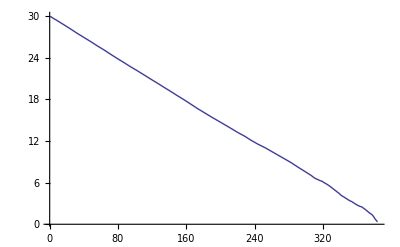

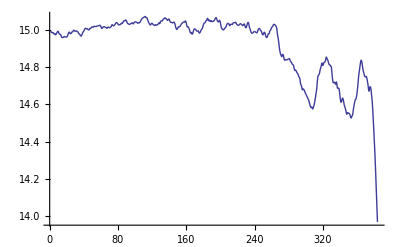

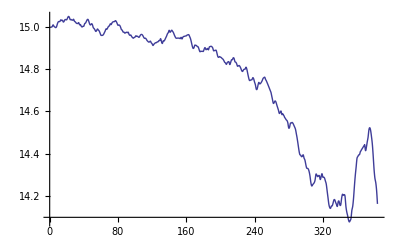

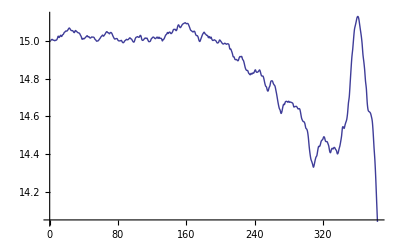

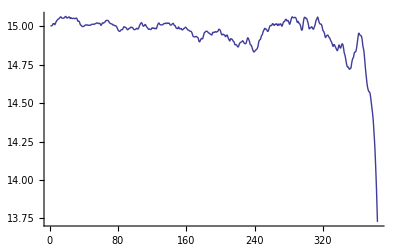

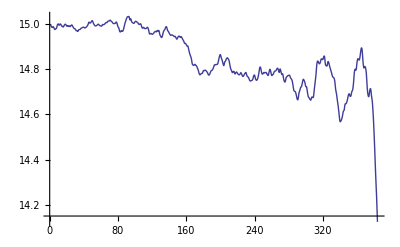

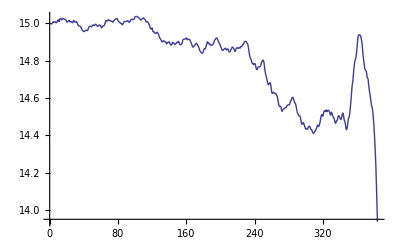

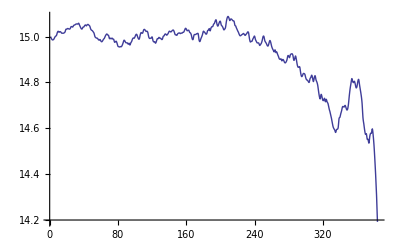

```mathematica
(*draw*)
φ1f=Interpolation[φ1];
φ2f=Interpolation[φ2];
φ3f=Interpolation[φ3];
φ4f=Interpolation[φ4];
φ5f=Interpolation[φ5];
φ6f=Interpolation[φ6];
φ7f=Interpolation[φ7];
φ8f=Interpolation[φ8];
φ9f=Interpolation[φ9];
φ10f=Interpolation[φ10];
φ11f=Interpolation[φ11];
φ12f=Interpolation[φ12];
φ13f=Interpolation[φ13];
φ14f=Interpolation[φ14];
φ15f=Interpolation[φ15];
φ16f=Interpolation[φ16];
φ17f=Interpolation[φ17];
φ18f=Interpolation[φ18];
φ19f=Interpolation[φ19];
φ20f=Interpolation[φ20];
plot1=Plot[φ1f[x],{x,1,i}, PlotRange->All]
plot2=Plot[φ2f[x],{x,1,i},PlotRange->All]
plot3=Plot[φ3f[x],{x,1,i},PlotRange->All]
plot4=Plot[φ4f[x],{x,1,i},PlotRange->All]
plot5=Plot[φ5f[x],{x,1,i},PlotRange->All]
plot6=Plot[φ6f[x],{x,1,i},PlotRange->All]
plot7=Plot[φ7f[x],{x,1,i},PlotRange->All]
plot8=Plot[φ8f[x],{x,1,i},PlotRange->All]
plot9=Plot[φ9f[x],{x,1,i},PlotRange->All]
plot10=Plot[φ10f[x],{x,1,i},PlotRange->All]
plot11=Plot[φ11f[x],{x,1,i},PlotRange->All]
plot12=Plot[φ12f[x],{x,1,i},PlotRange->All]
plot13=Plot[φ13f[x],{x,1,i},PlotRange->All]
plot14=Plot[φ14f[x],{x,1,i},PlotRange->All]
plot15=Plot[φ15f[x],{x,1,i},PlotRange->All]
plot16=Plot[φ16f[x],{x,1,i},PlotRange->All]
plot17=Plot[φ17f[x],{x,1,i},PlotRange->All]
plot18=Plot[φ18f[x],{x,1,i},PlotRange->All]
plot19=Plot[φ19f[x],{x,1,i},PlotRange->All]
plot20=Plot[φ20f[x],{x,1,i},PlotRange->All]
```